## Basics

```mathematica
ReadGrof[n_]:=Block[{fileName,l,f, str},
fileName = "D:\\Grofs\\"<> ToString[n] <> ".grof";
f=OpenRead[fileName,BinaryFormat->False];
l=ReadList[f,"String",1,RecordSeparators->{"\r\n","\r" }];
l="{"<>l[[1]]<>"}";
str=StringToStream[l];
l=ReadList[str,Expression,1];
Close[str];
Close[f];
Return[Graph[l[[1]]]]
]
```

```mathematica
ReadFaces[n_]:=Block[{fileName,l,f,line, result, lines},
result={};
fileName = "D:\\Grofs\\Faces\\"<> ToString[n] <> ".face";
lines=ReadList[fileName,Record];
result=Map[
With[{str=StringToStream["{"<>#<>"}"]},
l=ReadList[str,Expression][[1]];
Close[str];
l
]&,lines];
(* first item is face id, then 3 vertices of the face, then the face ids of the neighbours *)
result=Map[Take[#,{2,4}]&,result];
Return[result]
]
```

```mathematica
ReadGraphDiamond[n_]:=Block[
{f, l},
f=OpenRead["d:\\grofs\\diamonds\\"<>ToString[n]<>".diamond"];
l=ReadList[f,"String",1,RecordSeparators->{"\r\n","\r" }];
Close[f];
l="{"<>l[[1]]<>"}";
l=ReadList[StringToStream[l],Expression,1];
Return[l[[1]]]
]
```

```mathematica
ReadGraphDiamondHighLights[n_]:=Block[
{f, l, result, chunk, colors =ColorData[109,"ColorList"], i},
result={};
f=OpenRead["d:\\grofs\\diamonds\\"<>ToString[n]<>".diamond"];
l=ReadList[f,"String",20,RecordSeparators->{"\r\n","\r" }];
result=Table[Read[StringToStream["{"<>k<>"}"]],{k,l}];
result=Table[Style[result[[i]],Thick,colors[[i]]],{i,1,Length[result]}];
Close[f];
Return[result]
]
```

```mathematica
CloseAll[]:=Map[Close[#]&,Cases[Streams[],_InputStream]]
```

## Bounds

```mathematica
Jacobsthal=LinearRecurrence[{2,1,-2},{0,2,1},50]
```

{0,2,1,4,5,12,21,44,85,172,341,684,1365,2732,5461,10924,21845,43692,87381,174764,349525,699052,1398101,2796204,5592405,11184812,22369621,44739244,89478485,178956972,357913941,715827884,1431655765,2863311532,5726623061,11453246124,22906492245,45812984492,91625968981,183251937964,366503875925,733007751852,1466015503701,2932031007404,5864062014805,11728124029612,23456248059221,46912496118444,93824992236885,187649984473772}

```mathematica
CountMPG={2,2,5,14,50,233,1249,7595,49566,339722}
```

{2,2,5,14,50,233,1249,7595,49566,339722}

```mathematica
EndMPG=Accumulate[CountMPG]
```

{2,4,9,23,73,306,1555,9150,58716,398438}

```mathematica
StartMpg=Join[{1},EndMPG+1]
```

{1,3,5,10,24,74,307,1556,9151,58717,398439}

```mathematica
mpgBounds=Table[{StartMpg[[k]],EndMPG[[k]]},{k,1,9}]
```

{{1,2},{3,4},{5,9},{10,23},{24,73},{74,306},{307,1555},{1556,9150},{9151,58716}}

## Colofouring

```mathematica
Chromial[n_]:=Chromial[n]=ChromaticPolynomial[ReadGrof[n],x]
```

```mathematica
Chrom[n_]:=Chrom[n]=ChromaticPolynomial[ReadGrof[n],4]
```

```mathematica
Get["D:\\pre398438.m"];Length[pre];Table[Chrom[k]=pre[[k]],{k,1,Length[pre]}];"DONE"
```

Get::noopen: Cannot open D:\pre398438.m.

DONE

```mathematica
chroms=Keys[Get["d:\\chroms.m"]];Length[chroms]
```

Get::noopen: Cannot open d:\chroms.m.

Keys::invrl: The argument $Failed is not a valid Association or a list of rules.

1

```mathematica
(*Table[
pre=Monitor[Table[Chrom[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\pre-" <> ToString[max]<> ".txt"];
Save["D:\\pre" <> ToString[max]<> ".m",{pre}]; Print[max];max,
{max,Range[265000,300000,5000]}
]*)
```

## Colofiving

```mathematica
Chrom5[n_]:=Chrom5[n]=ChromaticPolynomial[ReadGrof[n],5]
```

```mathematica
Get["D:\\five398438.m"];Length[five];Table[Chrom5[k]=five[[k]],{k,1,Length[five]}];"DONE"
```

Get::noopen: Cannot open D:\five398438.m.

DONE

```mathematica
(*Table[
five=Monitor[Table[Chrom5[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\five" <> ToString[max]<> ".m"];
Save["D:\\five" <> ToString[max]<> ".m",{five}]; Print[max];max,
{max,Range[25000,100000,25000]}
]*)
```

```mathematica
MaxFive[n_]:=(-5 (-1)^n+2^(1+n)+5 3^n)/12
```

## ColoThree

```mathematica
Chrom3[n_]:=Chrom3[n]=ChromaticPolynomial[ReadGrof[n],3]
```

```mathematica
Get["D:\\three398438.m"];Length[three];Table[Chrom3[k]=three[[k]],{k,1,Length[three]}];"DONE"
```

Get::noopen: Cannot open D:\three398438.m.

DONE

```mathematica
(*Table[
five=Monitor[Table[Chrom5[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\five" <> ToString[max]<> ".m"];
Save["D:\\five" <> ToString[max]<> ".m",{five}]; Print[max];max,
{max,Range[25000,100000,25000]}
]*)
```

```mathematica
MaxFive[n_]:=(-5 (-1)^n+2^(1+n)+5 3^n)/12
```

## Rules

```mathematica
Rule1[g_,v1_, v2_,v3_]:= Block[{new, result=g},
new=Max[VertexList[g]]+1;
result=EdgeAdd[result,{v1<->new,v2<->new,v3<->new}];
result]
```

```mathematica
Rule2[g_,e_, e2_]:= Block[{new, result, start = e[[1]], stop=e[[2]], start2 = e2[[1]], stop2=e2[[2]]},
new=Max[VertexList[g]]+1;
result=EdgeDelete[g,e];
result=VertexAdd[result,new];
result=EdgeAdd[result,{start<->new,stop<->new,start2<->new,stop2<->new}];
result]
```

```mathematica
Rule3[g_,edges_,circle_]:=Block[{result,newNode},
newNode=Max[VertexList[g]]+1;
result=EdgeDelete[g,edges];
result=EdgeAdd[result,Table[v<->newNode,{v,circle}]];
result
]
```

## Reductions

```mathematica
ContainsRule1Reduction[n_]:= ContainsRule1Reduction[n]=Block[{interesting, found=False, g=ReadGrof[n]},
interesting=Table[v,{v,Select[VertexList[g],VertexDegree[g,#]==3&]}];
Table[If[MaximalPlanarQ[VertexDelete[g,v]],found=True],{v,interesting}];
Return [found]
]
```

```mathematica
redcount=ReadList["D:\\containsrule1red-50000.txt"];Length[redcount];Table[ContainsRule1Reduction[k]=redcount[[k]],{k,1,Length[redcount]}];"DONE"
```

ReadList::noopen: Cannot open D:\containsrule1red-50000.txt.

DONE

```mathematica
(*Table[
redcount=Monitor[Table[ContainsRule1Reduction[k],{k,1,max}],{k,N[k/max * 100]}];
PrintTemporary["Saving D:\\containsrule1red-" <> ToString[max]<> ".txt"];
Export["D:\\containsrule1red-" <> ToString[max]<> ".txt",redcount,"Table"]; Print[max];max,
{max,Range[1,58716,58716-1]}
]*)
```

## Drawing

```mathematica
ToVars[g_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
(* works only for graphs in which 1,2 and 3 are connected *)
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> "x1 == 1 && x2== 2 && x3==3";
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
ToEquations[g_]:=Block[{exp,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp=True;
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var =Symbol["x" <> ToString[ vertices[[vertex]] ]];
exp= exp&& Element[var, Integers];
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var =Symbol["x" <> ToString[ vertices[[vertex]] ]];
exp= exp&& (1≤var <=4);
];

edges=EdgeList[g];

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 =Symbol["x" <> ToString[ edge[[1]] ]];
var2 =Symbol["x" <> ToString[ edge[[2]] ]];
exp= exp&& var1!=var2;
];
exp
]
```

```mathematica
ToColors[l_]:=Block[{index, val, color, var, result},
result={};
For[index=1,index≤Length[l],index++,
var =ToExpression[ StringDrop [ToString[l[[index,1]]],1]];
color= IndexToColor [l[[index,2]] ];
AppendTo[result,var->color]
];
result
]
```

```mathematica
IndexToColor[i_]:={Red,Green,Blue, Yellow}[[i]]
```

```mathematica
ListToColor[l_]:=Map[IndexToColor[#]&,l]
```

```mathematica
ToColors2[assoc_]:=Map[#->IndexToColor[assoc[#]]&,Keys[assoc]]
```

```mathematica
PaintGraph[g_, opts__]:=Block[{sols},
sols=ToVars[g];
{Map[
VertexDelete[Graph[g,PlotLabel->ChromaticPolynomial[g,4],ImageSize->250, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#], VertexLabels->"Name", VertexSize->Medium, opts],{1,2,3}]&
,sols],
Map[
Graph[g,PlotLabel->ChromaticPolynomial[g,4],ImageSize->250, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#], VertexLabels->"Name", VertexSize->Medium, opts]&
,sols]}
]
```

## Drawing Part 2

```mathematica
ToVars2[g_, pre_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> pre;(* "x1 == 1 && x2== 2 && x3==3";*)
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
Criterion[edge1_,edge2_]:="x"<>ToString[edge1[[1]]]<>"==1&&x"<>ToString[edge1[[2]]]<>"==2&&x"<>ToString[edge2[[1]]]<>"==3"
```

```mathematica
PaintGraph2[g_,pre_, opts__]:=Block[{sols},
sols=ToVars2[g,pre];
Map[
Graph[
(*Print[Map[Last,ToColors[Sort[#]]]//Row];*)g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#],  VertexSize->Medium]&
,sols]
]
```

```mathematica
GraphSolutions[g_,pre_]:=Block[{sols},
sols=ToVars2[g,pre];
Map[Map[Last,ToColors[Sort[#]]]&
,sols]
]
```

```mathematica
PaintGraph2First[g_,pre_, opts__]:=Block[{sols},
sols=ToVars2[g,pre];
Graph[g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[sols[[1]]],  VertexSize->Medium]
]
```

## Constraints

```mathematica
SymbolComp[x_,y_]:=Block[{a,b},
a=FromDigits[StringDrop[SymbolName[x],1]];
b=FromDigits[StringDrop[SymbolName[y],1]];
a<b
]
```

```mathematica
ToLogical[g_]:=Block[{exp,vertex,vertices,var,var1,var2,edges,edgeIndex,edge},exp=True;
vertices=VertexList[g];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&Element[var,Integers];];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&(1≤var≤4);];
edges=EdgeList[g];
For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,edge=edges[[edgeIndex]];
var1=Symbol["x"<>ToString[edge[[1]]]];
var2=Symbol["x"<>ToString[edge[[2]]]];
exp=exp&&var1≠var2;];
exp]
```

```mathematica
ToVarsLogical[g_, pre_]:=Block[{exp},
exp= ToLogical[g]&&pre;
Solve[exp,SymbolRange[g]]
]
```

```mathematica
PaintGraph3[g_,pre_, opts__]:=Block[{sols},
sols=ToVarsLogical[g,pre];
Map[
Graph[
g,opts, GraphLayout->"PlanarEmbedding", VertexStyle->ToColors[#],  VertexSize->Medium]&
,sols]
]
```

```mathematica
SymbolRange[g_]:=Table[Symbol["x" <> ToString[ k ]],{k,VertexList[g]}]
```

```mathematica
GraphSolutions2[g_, cycle_]:=Block[{sols, cond},
cond=ToLogical[g];
(*cond=Symbol["x"<>ToString[cycle[[1]]]] ==1 && Symbol["x"<>ToString[cycle[[2]]]] ==2 && cond;*)
sols=Solve[cond,SymbolRange[g]];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

```mathematica
GraphSolutions2[g_]:=Block[{sols, cond},
cond=ToLogical[g];
(*cond=Symbol["x"<>ToString[cycle[[1]]]] ==1 && Symbol["x"<>ToString[cycle[[2]]]] ==2 && cond;*)
sols=Solve[cond,SymbolRange[g]];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

```mathematica
GraphSolutions3[g_,pre_]:=Block[{sols, cond},
sols=ToVarsLogical[g,pre];
Map[Sort[#,SymbolComp[#1[[1]],#2[[1]]]&]&,sols]
]
```

## Unique rule 2

```mathematica
maxDep=100
```

100

```mathematica
deps1=ReadList["D:\\Grofs\\dependencies1.txt",Expression,maxDep];Length[deps1]
"OK"
```

ReadList::noopen: Cannot open D:\Grofs\dependencies1.txt.

0

OK

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression,maxDep];Length[deps2]
```

ReadList::noopen: Cannot open D:\Grofs\dependencies2.txt.

0

```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression,maxDep];Length[deps3]
```

ReadList::noopen: Cannot open D:\Grofs\dependencies3.txt.

0

```mathematica
EnrichDep[t_]:=Select[
Map[{#[[1]],#[[2]],Chrom[#[[1]]],Chrom[#[[2]]],#[[3]]}&,t], #[[3]]>#[[4]]&
]
```

```mathematica
Rule1Sources[level_]:=With[
{from=mpgBounds[[level,1]],to=mpgBounds[[level,2]]},
Sort[DeleteDuplicates[Map[First,Take[deps1,{from,to}]]]]
]
```

```mathematica
Rule1Sources[from_,to__]:=Sort[DeleteDuplicates[Map[First,Take[deps1,{from,to}]]]]
```

```mathematica
Rule1Sinks[level_]:=With[
{from=mpgBounds[[level,1]],to=mpgBounds[[level,2]]},
Sort[DeleteDuplicates[Map[#[[2]]&,Take[deps1,{from,to}]]]]
]
```

```mathematica
Rule1Sinks[from_,to__]:=Sort[DeleteDuplicates[Map[#[[2]]&,Take[deps1,{from,to}]]]]
```

```mathematica
Rule1SinksRecursive[level_]:=Block[
{current, currentLevel, bounds},
current = Rule1Sinks[1];
For[currentLevel=2,currentLevel<=level,currentLevel++,
bounds=mpgBounds[[currentLevel]];
current=Sort[
DeleteDuplicates[
Map[#[[2]]&,
Select[ Take[deps1,bounds],MemberQ[current,#[[1]]]&]
]
]
]
];
current
]
```

## Search

```mathematica
FindGraph[g_,from_,to_]:=Block[{i, found=-1},Monitor[For[i=from,i≤to,i++,
If[IsomorphicGraphQ[ReadGrof[i],g],found=i;Break[]]
],{from,i,to}
];
Return[found]
]
```

## Planarity

```mathematica
MaximalPlanarQ[g_]:=Block[{gs},
If[!PlanarGraphQ[g],Return[False]];
gs=EdgeAdd[g,#]&/@EdgeList[GraphComplement[g]];
If[Length[gs]==1,!PlanarGraphQ[gs[[1]]],Not[PlanarGraphQ/@(Or@@gs)]]
]
```

## JacobsthalGraph

```mathematica
JacobsThalGraph[n_]:=With[{max=4+n},Graph[DeleteDuplicates[Join[{1<->2,3<->2,3<->1,1<->4,2<->4,5<->1,max<->2,max<->3},Flatten[Table[{i<->i-1,i<->3,i<->4},{i,5,max}]]]]]]
```

```mathematica
JacobsThalQ[g_]:= AnyTrue[Table[IsomorphicGraphQ[JacobsThalGraph[k],g],{k,1,15}],TrueQ]
```

```mathematica
JacobsThalGraph2[n_]:=If[n<=4,CompleteGraph[n],JacobsThalGraph[n-4]]
```

## Diamond

```mathematica
DiamondGraph[n_]:=With[
{max=2+n},
Graph[
Range[max]
,
DeleteDuplicates[
Join[
Flatten[Table[{1<->i,2<->i},{i,3,max}]],
Flatten[Table[{i<->i+1,2<->i},{i,3,max-1}]]
]
],
VertexCoordinates->Join[{{(n+1)/2,2},{(n+1)/2,-2}},Table[{i-2,0},{i,3,max}]]
]
]
```

## Signature

```mathematica
GraphSignature[k_]:=With[{g=ReadGrof[k]},
StringRiffle[ Sort[VertexDegree[g],Greater],"-"]
]
```

```mathematica
GraphSignature2[g_]:=StringRiffle[ Sort[VertexDegree[g],Greater],"-"]
```

## Cycles

### The cyclemat computes a matrix. Each row corresponds to a vertex. Each column k corresponds to the number of cycles of length k in which that vertex participates. For the moment it turned out to be of limited usage.

```mathematica
CycleMat[g_]:=Block[
{cycles,vertexCount=VertexCount[g],result, k,l,m, current,currentLength, first, second, pair},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[Table[0,{i,1,vertexCount}],{j,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
currentLength=Length[current];
For[m=1,m≤currentLength,m++,
pair=current[[m]];
first=pair[[1]];
second=pair[[2]];
result[[first,currentLength]]++;
result[[second,currentLength]]++;
]
];
result/2 (* each vertex counted twice *)
]
```

### The edgecyclemat computes an association. The key of the association are the edges of the input graph. For each of them we compute a vector. The kth value of the vector is the number of k-length cycles in which that edge participates.

```mathematica
EdgeCycleMat[g_]:=Block[
{cycles,vertexCount=VertexCount[g],result, k,l,m, current,currentLength, line, pair},
cycles=FindCycle[g,{2,vertexCount},All];
result=Association[Table[Sort[e]->Table[0,{i,1,vertexCount}],{e,EdgeList[g]}]];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
currentLength=Length[current];
For[m=1,m≤currentLength,m++,
pair=Sort[current[[m]]];
line=result[pair];
line[[currentLength]]++;
result[pair]=line
]
];
result
]
```

### The vertexcyclevect computes a vector for the given vertices. The kth value of the vector is the number of k-length cycles in which both vertices participate.

```mathematica
VertexCycleVect[g_, vertex1_, vertex2_]:=Block[
{cycles,vertexCount=VertexCount[g],result,result2, k,l,m, current,currentLength},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[0,{i,1,vertexCount}];
result2=Table[{},{i,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
If[(MemberQ[current,vertex1<->_])&&(MemberQ[current,vertex2<->_]),
currentLength=Length[current];
result[[currentLength]]++;
AppendTo[result2[[currentLength]],current];
]
];
result
]
```

### The following takes as input a list as generated by rule2. Elements look like {7,21,”{2,2<->6,3<->5}”}. This means that there is a rule 2 transition from graph 7 to graph 21. The existing edge on graph 7 on which we apply the rule is 2<->6. 3<->5 are the other vertices (not connected) in the rule 2 transition. For each of them we computed the vertexcyclevect.

```mathematica
ExplainRule2WithCycles[list_]:=Block[
{l, result, chunk, colors =ColorData[1,"ColorList"],
 i},
result={};
result=Table[
With[
{record=Read[StringToStream[list[[i,3]]]]},
With[
{g=ReadGrof[list[[i,1]]]},
{(Chrom[list[[i,2]]]/24)-(Chrom[list[[i,1]]]/24),
list[[i,1]]->(Chrom[list[[i,1]]]/24),
list[[i,2]]->(Chrom[list[[i,2]]]/24),
{record[[2]]}->VertexCycleVect[g,record[[2,1]],record[[2,2]]],
{record[[3]]}->VertexCycleVect[g,record[[3,1]],record[[3,2]]]
} 
]
],{i,1,Length[list]}];
Return[Sort[result]]
]
```

## Cycle polynomial

### The cyclemat computes a matrix. Each row corresponds to a vertex. Each column k corresponds to the number of cycles of length k in which that vertex participates. For the moment it turned out to be of limited usage.

```mathematica
NullBaseCoeff[p_]:=CoefficientList[p,x]
```

```mathematica
CyclePoly[1]:=x
```

```mathematica
CyclePoly[n_]:=CyclePoly[n]=ChromaticPolynomial[CycleGraph[n],x]
```

```mathematica
CycleBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = CyclePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
CompletePoly[n_]:=CompletePoly[n]=Product[x-i,{i,0,n-1}]//Expand
```

```mathematica
CompleteBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = CompletePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
PathPoly[n_]:=PathPoly[n]=ChromaticPolynomial[PathGraph[Range[n]],x]
```

```mathematica
PathBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = PathPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
JacobsthalPoly[n_]:=JacobsthalPoly[n]=ChromaticPolynomial[JacobsThalGraph2[n],x]
```

```mathematica
JacobsthalBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = JacobsthalPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
TreePoly[n_]:=TreePoly[n]=x(x-1)^n
```

```mathematica
TreeBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=1,pos≤degree,pos++,
current = TreePoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

## Polynomial base conversion

### Create a matrix that, when applied to the coefficients of a normal (null base) polynomial will produce the coefficients in the cycle base.

```mathematica
FromNormalToCycle[n_]:=Block[{result,k,l},
result=Table[0,{i,1,n},{j,1,n}];
For[k=1,k≤n-1,k++,
For[l=1,l≤n-1,l++,
result[[k+1,l+1]]=Binomial[k,l]
]
];
For[k=2,k≤n,k++,
result[[k,2]]=2^(k-2)
];
result[[1,1]]=1;
result
]
```

```mathematica
FromNormalToComplete[length_]:= Table[If[i==j==1,1,If[i==1||j==1,0,StirlingS2[i-1,j-1]]],{i,1,length},{j,1,length}]
```

```mathematica
FromCompleteToNormal[length_]:= Table[If[i==j==1,1,If[i==1||j==1,0,StirlingS1[i-1,j-1]]],{i,1,length},{j,1,length}]
```

## Matrices

```mathematica
DistanceMatrix[g_]:=Block[{result, count, i, vertices},
count=VertexCount[g];
vertices=VertexList[g];
result=Table[
With[
{p=FindShortestPath[g,vertices[[i]],vertices[[j]]]},
Length[p]-1
]
,{i,1,count},{j,1,count}];
result
]
```

SetDelayed::write: Tag DistanceMatrix in DistanceMatrix[g_] is Protected.

$Failed

## Helpers

```mathematica
Rule3Cycle[l_]:=Block[{result},
result= Table[l[[i]]<->l[[i+1]],{i,1,Length[l]-1}];
result=Join[result,{l[[1]]<->l[[Length[l]]]}];
result
]
```

## Inner/Outer pentagons

```mathematica
Succ[n_,max_]:=Mod[n,max]+1
```

```mathematica
Pred[n_,max_]:=Mod[max+n-2,max]+1
```

### Create a graph with an inner and an outer “pentagon”. The counts are the number of intermediary nodes.

```mathematica
MakeInnerOuterGraph[counts_]:=Block[{len=Length[counts],result, current,previous=-1, inner=1,zone,prevInner},

result=Table[i<->Succ[i,len],{i,len}];
current=len+1;
prevInner=len;
For[inner=1,inner≤len,inner++,
For[zone=0,zone≤counts[[inner]],zone++,
AppendTo[result,current<->inner];
If[previous ≠-1,
AppendTo[result,current<->previous];
];
If[prevInner ≠-1,
AppendTo[result,current<->prevInner];
prevInner=-1;
];
previous=current;
current++;
];
prevInner=inner;
];
AppendTo[result,current-1<->len+1];
(*AppendTo[result,current-1<->1];*)
result
]
```

## PRO graphs

```mathematica
FindCommonNeighbour[g_,v1_,v2_]:=Block[{temp},
temp=VertexDelete[NeighborhoodGraph[g,v1],v1];
temp=VertexDelete[NeighborhoodGraph[temp,v2],v2];
First[VertexList[temp]]
]
```

```mathematica
DiscoverCycle[g_,vertices_]:=Block[{result={},sorted=Sort[vertices], i, first,temp},
While[sorted≠{},
first=sorted[[1]];
sorted=Drop[sorted,1];
For[i=1,i≤Length[sorted],i++,
If[EdgeQ[g,first<->sorted[[i]]],
AppendTo[result,first<->sorted[[i]]];
temp=sorted[[1]];
sorted[[1]]=sorted[[i]];
sorted[[i]]=temp;
i=100;
]
];
];
AppendTo[result,First[result][[1]]<->Last[result][[2]]];
result
]
```

```mathematica
DiscoverOuterVertices[g_,innerEdges_]:=Block[{result={}},
Table[With[{h=FindCommonNeighbour[g,e[[1]],e[[2]]]},h],{e,innerEdges}]
]
```

```mathematica
ContractPentagons[g_]:=Block[{vertices,neighbours,h,innerEdges,outerVertices,outerEdges,common, outerSorted,f,i,steps={}},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
Table[
neighbours=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,EdgeList[g,center<->_]]],#≠center&]];
innerEdges=DiscoverCycle[g,neighbours];
h=VertexDelete[g,center];
outerVertices=DiscoverOuterVertices[h,innerEdges];
common=FindCommonNeighbour[h,innerEdges[[1,1]],innerEdges[[1,2]]];
outerSorted=Table[FindCommonNeighbour[h,e[[1]],e[[2]]],{e,innerEdges}];
outerEdges=DiscoverCycle[g,outerVertices];
f=VertexDelete[g,center];
AppendTo[steps,Graph[g,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
]];
AppendTo[steps,Graph[f,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
]];
For[i=1,i≤Length[neighbours],i++,
f=VertexContract[f,{neighbours[[i]],outerSorted[[i]]}];
AppendTo[steps,Graph[f,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
]]
];
(*Print[steps];
h=Graph[f,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,outerEdges]],
VertexStyle->Map[#->{Thick,Yellow}&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
ImageSize->200
];
h*)
steps
,{center,{First[vertices]}}
]
]
```

```mathematica
FindFace[g_,e_]:=Block[{h,n1,n2,i},
h=EdgeDelete[g,e];
n1=NeighborhoodGraph[h,e[[1]]];
n2=NeighborhoodGraph[h,e[[2]]];
i=Intersection[VertexList[n1],VertexList[n2]];
{e[[1]],i[[1]],e[[2]],i[[2]]}
]
```

```mathematica
plantri=ReadList["D:\\min5.txt",Expression,100000];Length[plantri]
```

100000

```mathematica
FindPlantri[g_,from_,to_]:=Block[{i, found=-1},Monitor[For[i=from,i≤to,i++,
If[IsomorphicGraphQ[Graph[plantri[[i]]],g],found=i;Break[]]
],{from,i,to}
];
Return[found]
]
```

### For a pro grpah, discover the pentagon vertices around the inner pentagon, given by the vertices and edges. The returned list is a set of edges in arbitrary order

```mathematica
DiscoverOuterPentagon[g_,innerVertices_, innerEdges_]:=Block[{result={},  inner=innerVertices,h=EdgeDelete[g,innerEdges],neighbours},
Table[
neighbours=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,EdgeList[h,innerVertex<->_]]],#≠innerVertex&]];
result=Join[result,neighbours]
,{innerVertex, innerVertices}
];
DeleteDuplicates[result]
]
```

### Create a graph with an inner and an outer “pentagon”, ready for painting. We pick an arbitrary nodes with degree 5 to start from

```mathematica
DeleteHeartAndPaint[g_]:=Block[{vertices,innerVertices,center,h,innerEdges,outerVertices,outerEdges, completeOuter, completeOuterEdges},
vertices=Select[VertexList[g],VertexDegree[g,#]==5&];
center=First[vertices];
innerVertices=DeleteDuplicates[Select[Flatten[Map[{#[[1]],#[[2]]}&,EdgeList[g,center<->_]]],#≠center&]];
innerEdges=DiscoverCycle[g,innerVertices];
h=VertexDelete[g,center];
outerVertices=DiscoverOuterVertices[h,innerEdges];
outerEdges=DiscoverCycle[g,outerVertices];
completeOuter=DiscoverOuterPentagon[h,innerVertices,innerEdges];
completeOuterEdges=DiscoverCycle[g,completeOuter];
Graph[h,
EdgeStyle->Join[Map[#->{Thick,Red}&,innerEdges],Map[#->{Thick,Darker[Green]}&,completeOuterEdges]],
VertexShape->Map[#->Graphics[{EdgeForm[{Thick,Blue}],Yellow,Disk[{0,0},20]}]&,outerVertices],
GraphLayout->"TutteEmbedding",
VertexSize->Large,
VertexLabels->"Name",
ImageSize->400
]
]
```

## Compatibility matrix

The following code builds a matrix that compares the possible color combinations for each vertex pair (even those not connected) before and after an operation.  The result is formatted as a graph.

```mathematica
FindGraphInSet[g_,set_]:=Block[{result=-1},
For[k=1,k≤Length[set],k++,
If[IsomorphicGraphQ[g,set[[k]]],result=k;Break[]]
];
result
]
```

```mathematica
ColorsForEdgeOperationMatrix[g_,edges_,operation_]:=Block[{ sols,sols2,h, result,mat,mat2,bg,bigResult,one,two,three,first2,second2},
one=Graph[{1<->1,2<->2,3<->3,4<->4}];
two=CompleteGraph[4];
three=EdgeAdd[ two,EdgeList[one]];
PrintTemporary["Solving g.."];
sols=Solve[ToEquations[g],SymbolRange[g]];
PrintTemporary["Solved g"];
Monitor[
bigResult=Table[
PrintTemporary["Solving h.." <> ToString[e]];
h=operation[g,e];
sols2=Solve[ToEquations[h],SymbolRange[h]];
PrintTemporary["Solved h "  <> ToString[e]];
result=MatrixForm[
Table[
bg=None;
Framed[
With[
{first=If[
VertexQ[g,i]&&VertexQ[g,j],
Graph[DeleteDuplicates[Map[Sort[{Symbol["x"<>ToString[i]],Symbol["x"<>ToString[j]]}/.#]&,sols]],ImageSize->20, DirectedEdges->False],
"ϵ"],
second=If[
VertexQ[h,i]&&VertexQ[h,j],
Graph[DeleteDuplicates[Map[Sort[{Symbol["x"<>ToString[i]],Symbol["x"<>ToString[j]]}/.#]&,sols2]],ImageSize->20, DirectedEdges->False],
"ϵ"
]
},
If[EdgeQ[first,1<->1],bg=LightPurple];
If[EdgeQ[second,1<->1],bg=LightGreen];
If[EdgeQ[g,i<->j],bg=LightBlue;If[!EdgeQ[h,i<->j],bg=LightRed;]];
If[i==j,bg=LightYellow];
first2=FindGraphInSet[first,{one,two,three}];
If[first2==-1,first2=first];
second2=FindGraphInSet[second,{one,two,three}];
If[second2==-1,second2=second];
If[first2==second2,first2,
first2->second2
]
],
Background->bg
],
{i,VertexList[g]},
{j,VertexList[g]}],
TableHeadings->{VertexList[g], VertexList[g]},
TableSpacing->{0, 0}
];
Labeled[result,{operation,e}],
{e,edges}
],
{operation,e,i,j}
];
bigResult
]
```

```mathematica
ColorSubMatrix[sols_,e1_,e2_]:=Block[{subList,result},
subList=Map[{Symbol["x"<>ToString[e1]],Symbol["x"<>ToString[e2]]}/.#&,sols];
result=Table[With[{color1=i[[1]],color2=i[[2]]},
Length[Select[subList,#[[1]]==color1&&#[[2]]==color2&]]*i[[3]]
],
{i,{{1,1,1/6},{1,2,1/2}}}];
result
]
```

```mathematica
DoNothing[g_,e_]:=g
```

```mathematica
ColorMainMatrix[graph_,graphFormat_:FormatGraph,vertices_:Null]:=Block[{sols,result,bg, sorted},
PrintTemporary["Solving g.." ];
sorted=Graph[Sort[VertexList[graph]],Sort[EdgeList[graph],EdgeComp]];
sols=Solve[ToEquations[sorted],SymbolRange[sorted]];
PrintTemporary["Solved g" ];
result=TableForm[
Table[
bg=None;
If[i≤j,
Framed[
With[
{
mat=ColorSubMatrix[sols,i,j]
},

If[mat[[1]]==0,bg=LightRed];
If[MemberQ[vertices,i]&&MemberQ[vertices,j],bg=LightRed];
If[i==j,bg=LightYellow];
If[EdgeQ[sorted,i<->j],bg=LightBlue];
TableForm[mat]
],
Background->bg
],
""
],
{i,VertexList[sorted]},
{j,VertexList[sorted]}],
TableHeadings->{VertexList[sorted], VertexList[sorted]},
TableSpacing->{0, 0}
];
{graphFormat[sorted],result}
]
```

```mathematica
FormatGraph[g_]:=Graph[g,GraphLayout->"TutteeEmbedding",VertexLabels->"Name",PlotLabel->ChromaticPolynomial[g,4],ImageSize->300]
```

```mathematica
ColorMatrixForEdgeOperationMatrix[g_,edges_,ops_,graphFormat_ : FormatGraph,vertices_ : Null]:=Block[{ sols2,h, result,bg,bigResult},
Monitor[
bigResult=Prepend[
Table[
h=op[g,e];
result=ColorMainMatrix[h,graphFormat,vertices];
Labeled[result,{op,e}],
{e,edges},
{op, ops}
],Labeled[ColorMainMatrix[g,graphFormat,vertices],"full"]
],
{op,e,i,j}
];
bigResult
]
```

```mathematica
ColorsForEdgeDeleteMatrix[g_,edges_]:=ColorsForEdgeOperationMatrix[g,edges,EdgeDelete]
```

```mathematica
ColorsForEdgeContractMatrix[g_,edges_]:=ColorsForEdgeOperationMatrix[g,edges,EdgeContract]
```

```mathematica
EdgeComp[x_,y_]:=Block[{a,b},
a=Sort[{x[[1]],x[[2]]}];
b=Sort[{y[[1]],y[[2]]}];
If[a[[1]]<b[[1]],
True,
a[[2]]<b[[2]]
]
]
```

## Generating all graphs etc ...

```mathematica
CircleLayout[n_]:=Table[{Cos[(2π/n )(n-i+1)+Pi/2],Sin[(2π/n )(i-1)+Pi/2]},{i,n}]
```

```mathematica
totalDone=0;
```

```mathematica
GenAll[n_]:=Block[
{nodes},
totalDone=0;
nodes=Table[{i},{i,n}];
GenAllFromList[nodes]
]
```

```mathematica
PairWiseCombine[list_]:=Block[
{l=Length[list], sets,result={},temp,newItem},
sets=Subsets[Range[l],{2}];
result=Table[
temp=Table[k,{k,list}];
newItem=Sort[{s[[1]],s[[2]]}];
temp=Drop[temp,{newItem[[2]]}];
temp=Drop[temp,{newItem[[1]]}];
temp=Append[temp,Sort[Join[list[[newItem[[1]]]],list[[newItem[[2]]]]]]];
temp=Sort[temp];
temp
,
{s,sets}
];
result
]
```

```mathematica
MyCircle2[vertices_,length_]:=Block[{pos=N[ CircleLayout[length]], midPoint,temp,i,div},
midPoint=Mean[Table[pos[[v]],{v,vertices}]];
div=Sqrt[midPoint[[1]]^2+midPoint[[2]]^2];
If[True,
midPoint=pos[[vertices[[1]]]],
midPoint=midPoint/div
];
N[midPoint]
]
```

```mathematica
MyCircle[vertices_,length_]:=Block[{pos=N[ CircleLayout[length]], sum={0,0}},
Map[MyCircle2[#,length]&,vertices]
]
```

```mathematica
AllGraphs[list_]:=Block[
{l=Length[list],longLength=Total[Map[Length[#]&,list]], sets,result={},temp,g, mat, element, realResult},
(* subsets are the vertices that we will connect *)
sets=Subsets[Subsets[Range[l],{2}]];
Monitor[
result=Table[
(* create a matrix that is "not connected" *)
mat=Table[0,{i,longLength},{j,longLength}];
(* Mark everything within one bucket as "2" *)
Table[
Table[mat[[i,j]]=2;mat[[j,i]]=2,{i,list[[bucket]]},{j,list[[bucket]]}],
{bucket,l}
];

(* Mark everything for linked edges as "1" *)
Table[
Table[mat[[i,j]]=1;mat[[j,i]]=1,{i,list[[s2[[1]]]]},{j,list[[s2[[2]]]]}],
{s2,s}
];
g=Graph[Range[l],
Table[
s2[[1]]<->s2[[2]]
,{s2,s}
],
VertexLabels->Table[i->StringRiffle[ list[[i]],","],{i,l}],
VertexCoordinates->MyCircle[list,longLength],
VertexStyle->Red,
VertexSize->0.1,
EdgeStyle->{Thickness[0.02],Darker[Green]},
ImageSize->{50,50}
];
totalDone++;
element=Association[];
element["signature"]=GraphMatrixSignature[mat];
element["matrix"]=mat;
element["graph"]=g;
element["vertexsets"]=list;
element["vertices"]=Range[l];
element["edges"]=s;
element["relations"]={};
element["links"]={};
element
,
{s,sets}
];
realResult=Association[];
Table[
realResult[el["signature"]]=el,
{el,result}
];
realResult,
totalDone
]
]
```

```mathematica
GenAllFromList[{{4},{6},{1,3},{2,5}}]//First
```

{{4},{6},{1,3},{2,5}}

```mathematica
GenAllFromList[list_]:=Block[
{nodes,result},

result=AllGraphs[list];
If[Length[list]>1,
Table[
Table[
result[el["signature"]]=el,
{el,GenAllFromList[v]}
]
,
{v,PairWiseCombine[list]}
]
];
result
]
```

```mathematica
GraphMatrixSignature[matrix_]:=Block[{l=Length[matrix]},
FromDigits[
Flatten[
Table[Table[matrix[[i,j]],{j,i+1,l}],{i,1,l}]
],3]
]
```

```mathematica
GraphMatrixSignature2[matrix_,indexSet1_,indexSet2_, newValue_]:=Block[
{temp=matrix, result},
Table[
temp[[i2,j2]]=newValue;
temp[[j2,i2]]=newValue;
,{i2,indexSet1},{j2,indexSet2}];

Table[
temp[[i,i]]=2;
,{i,Length[temp]}];
result=GraphMatrixSignature[temp];
Print["---->", result, temp];
result
]
```

```mathematica
CompressGraph[full_,vertices_]:=Block[
{x,y,l=Length[vertices],a,b},
Table[
a=vertices[[i,1]];
b=vertices[[j,1]];
full[[a,b]]
,{i,l},{j,l}
]
]
```

```mathematica
UnCompressGraph[small_,vertices_]:=Block[
{x,l=Total[Map[Length[#]&,vertices]],a,b,result,l2=Length[vertices]},
result=Table[0,{i,l},{j,l}];
Table[
a=vertices[[i]];
b=vertices[[j]];
x=small[[i,j]];
Table[
result[[a1,b1]]=x,{a1,a},{b1,b}
]
,{i,l2},{j,l2}
];
result
]
```

```mathematica
GraphMatrixSignature2[currentCompressed_,i_,j_,value_,currentVertexSets_]:=Block[
{uncomp=currentCompressed,sig,mat,l=Length[currentCompressed],m},
(* if the value is 2 then we run over the columns i and j and assign the maximum of both columns to each.
  This makes sure that connected stays connected and merged stays merged *)
If[value==2,
Table[
m=Max[uncomp[[i,a]],uncomp[[j,a]]];
uncomp[[j,a]]=m;
uncomp[[i,a]]=m;

uncomp[[a,j]]=m;
uncomp[[a,i]]=m
,{a,l}];

(*Print["uncomp",i, "  ", j, "  ",sig, "  ",MatrixForm[uncomp]];*)

];
uncomp[[i,j]]=value;
uncomp[[j,i]]=value;
mat=UnCompressGraph[uncomp,currentVertexSets];
sig=GraphMatrixSignature[mat];
(*Print["uncompressed",i, "  ", j, "  ",sig, "  ",MatrixForm[currentCompressed]-> MatrixForm[mat]];*)
sig
]
```

```mathematica
CompleteRelations[assocs_]:=Block[
{current, currentGraph, currentID,currentMatrix,currentVertexSets, currentCompressed,one,two, relations={}, links,l, newAssocs=Association[],keep, count=0},
Monitor[
Table[
count++;
current=assocs[key];
currentGraph=current["graph"];
currentID=current["signature"];
currentMatrix=current["matrix"];
currentVertexSets=current["vertexsets"];
currentCompressed=CompressGraph[currentMatrix,currentVertexSets];
keep=currentCompressed;
l=Length[currentCompressed];
links={};
relations={};

Table[
currentCompressed=keep;
If[currentCompressed[[i,j]]==2,
(* current is contracted of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,1,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,0,currentVertexSets];


If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]-Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
,
If[currentCompressed[[i,j]]==1,
(* current is connected of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,2,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,0,currentVertexSets];


If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]-Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
,
(* current is unconnected of one and two *)
one=GraphMatrixSignature2[currentCompressed,i,j,2,currentVertexSets];
two=GraphMatrixSignature2[currentCompressed,i,j,1,currentVertexSets];
AppendTo[links,one];
AppendTo[links,two];

If[KeyExistsQ[assocs,two]&&KeyExistsQ[assocs,one],
AppendTo[relations,Symbol["x"<>ToString[key]]== Symbol["x"<>ToString[two]]+Symbol["x"<>ToString[one]]]
,
Print[one, "   ",KeyExistsQ[assocs,one],"  ", two, "   ",KeyExistsQ[assocs,two], "  ", currentMatrix//MatrixForm, "   ", keep//MatrixForm, "   ",i , "   ", j, "  3333 ", currentVertexSets];
Interrupt[]
]
]
]
,{i,1,l},{j,i+1,l}
];
current["relations"]=relations;
(*PrintTemporary[relations];*)
current["links"]=links;
newAssocs[key]=current
,
{key, Sort[Keys[assocs]]}
],
{count,key}];
newAssocs
]
```

```mathematica
SymbolComp[x_,y_]:=Block[{a,b,o,p},
a=StringTake[SymbolName[x],1];
b=StringTake[SymbolName[y],1];
If[a≠b,Return[a<b]];
o=FromDigits[StringPadLeft[StringDrop[SymbolName[x],1],3,"0"]];
p=FromDigits[StringPadLeft[StringDrop[SymbolName[y],1],3,"0"]];
Return[o<p]
]
TrueQ["c">"b"]
False
ExpComp[d1>0,d10>0]
False
LongSymbol[x_]:=Block[{comp, start,end},
comp=ToString[x];
start=StringTake[comp,1];
end=StringPadLeft[ StringDrop[comp,1],3,"0"];
start<>end
]
ExpComp[x_,y_]:=Block[{
varx=getAllVariables[x],
vary=getAllVariables[y],
o,p},
If[Length[varx]≠Length[vary],
Return [Length[varx]<Length[vary]]
];
varx=Sort[varx,SymbolComp];
vary=Sort[vary,SymbolComp];
o=StringJoin[Map[ LongSymbol,varx]];
p=StringJoin[Map[LongSymbol,vary]];
Order[o,p]>0
]
ExpressionToTable2[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]]//Simplify,{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

False

False

ExpComp[d1>0,d10>0]

False

```mathematica
ExpressionToTable[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]]//Simplify,{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
OnlyOnex[exp_]:=Block[{
v=getAllVariables[exp]},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==1
]
```

```mathematica
NotASingleX[exp_]:=Block[{
v=ListofVars[exp]//DeleteDuplicates},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==0
]
```

```mathematica
OnlyTwox[exp_]:=Block[{
v=getAllVariables[exp]},
Length[Select[v,StringTake[ SymbolName[#],1]=="x"&]]==2
]
```

```mathematica
OnlyXVar[exp_]:=Block[{
v=getAllVariables[exp]},
First[Select[v,StringTake[ SymbolName[#],1]=="x"&]]
]
```

```mathematica
XVar[exp_]:=Block[{
v=getAllVariables[exp]},
Select[v,StringTake[ SymbolName[#],1]=="x"&]
]
```

```mathematica
GraphMatrixSignature[({{2,0,1,1},{0,2,0,0},{1,0,2,2},{1,0,2,2}})]
```

110

```mathematica
AllGraphs[{{1},{2},{3,4}}]//DeleteDuplicates
```

<|2→<|signature→2,matrix→{{2,0,0,0},{0,2,0,0},{0,0,2,2},{0,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{},relations→{},links→{}|>,245→<|signature→245,matrix→{{2,1,0,0},{1,2,0,0},{0,0,2,2},{0,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2}},relations→{},links→{}|>,110→<|signature→110,matrix→{{2,0,1,1},{0,2,0,0},{1,0,2,2},{1,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,3}},relations→{},links→{}|>,14→<|signature→14,matrix→{{2,0,0,0},{0,2,1,1},{0,1,2,2},{0,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{2,3}},relations→{},links→{}|>,353→<|signature→353,matrix→{{2,1,1,1},{1,2,0,0},{1,0,2,2},{1,0,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{1,3}},relations→{},links→{}|>,257→<|signature→257,matrix→{{2,1,0,0},{1,2,1,1},{0,1,2,2},{0,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{2,3}},relations→{},links→{}|>,122→<|signature→122,matrix→{{2,0,1,1},{0,2,1,1},{1,1,2,2},{1,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,3},{2,3}},relations→{},links→{}|>,365→<|signature→365,matrix→{{2,1,1,1},{1,2,1,1},{1,1,2,2},{1,1,2,2}},graph→-Graphics-,vertexsets→{{1},{2},{3,4}},vertices→{1,2,3},edges→{{1,2},{1,3},{2,3}},relations→{},links→{}|>|>

```mathematica
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};

getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]

getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]

getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]

getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]

getAllVariables[other_]:=other
```

```mathematica
ListofVars[exp_]:=With[{kk=getAllVariables[exp]},If[ListQ[kk],kk,{kk}]]
```

```mathematica
CosyPrint[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[TableForm[Map[FullSimplify[#/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1]&,
current["relations"]]],FontSize->12, FontFamily->"Consolas"], "   ",
MatrixForm[current["matrix"]]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},Red]]]
]
```

```mathematica
CosyPrint2[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[TableForm[Map[FullSimplify[#]&,
current["relations"]]],FontSize->12, FontFamily->"Consolas"], "   ",
MatrixForm[current["matrix"]]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]/.replaceMents/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]]
]
```

```mathematica
SymbolComp2[x_,y_]:=Block[{n1=SymbolName[x],n2=SymbolName[y],a,b,h1,h2},
h1=StringTake[n1,1];
h2=StringTake[n2,1];
If[h1≠h2,
Return[h1<h2]
];
a=SymbolToKey[n1];
b=SymbolToKey[n2];
a<b
]
```

```mathematica
CoeffVector[v_]:=Table[Coefficient[ (v/.replaceMents)*24,v,1],{v,Sort[myVars,SymbolComp2]}]
```

```mathematica
CosyPrint3[key_]:=With[
{current=newAssoc[key]},
Column[
{
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[MatrixForm[Map[First,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], "="}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]],
Style[MatrixForm[Map[Last,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], {"≠"}}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
]
]
```

```mathematica
CosyPrint4[key_]:=With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{50,50}],"   ",
Graph[VertexList[current["graph"]],EdgeList[current["graph"]],GraphLayout->"TutteEmbedding",ImageSize->{50,50}],"   ",
Style[MatrixForm[Map[First,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], "="}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"],
Style[MatrixForm[Map[Last,current["colortable3"]],TableHeadings->{Map[#[[1]]<->#[[2]]&,Subsets[Range[5],{2}]], {"≠"}}, TableSpacing->{2, 3}],FontSize->10, FontFamily->"Consolas"]
}
],Style[
{current["signature"]->
If[KeyExistsQ[current,"comp"],current["comp"],GreaterEqual][TraditionalForm[current["colofour"]]
,0],If[KeyExistsQ[current,"compwhy"],current["compwhy"],""]},Red]]]
]
```

```mathematica
ComposeInEq[key_]:=Block[{current=newAssoc[key],op, table,result,colofour},
table=current["colortable3"];
op=current["comp"];
colofour=current["colofour"];
DeleteDuplicates[
Flatten[
Table[
result=Join[
Table[With[{eq=table[[k,1]],noteq=table[[k,2]]},
If[NumberQ[eq]||NumberQ[noteq],
True,
{(op[eq,0]||op[noteq,0]),(eq≥0),(noteq≥0)}
]
],{k,1,10}]
,{op[colofour,0]}];
result
,
{comp,Subsets[Range[5],{2}]}]
]
]
]
```

```mathematica
ComposeInEq2[key_, hardFacts_]:=Block[{current=newAssoc[key],op, table,result,colofour},
table=current["colortable3"];
op=current["comp"];
colofour=current["colofour"];
DeleteDuplicates[
Flatten[
Table[
result=Join[
Table[With[{eq=table[[k,1]],noteq=table[[k,2]]},
If[NumberQ[eq]||NumberQ[noteq],
True,
{(Simplify[op[eq,0]||op[noteq,0]&& hardFacts]),(eq≥0),(noteq≥0)}
]
],{k,1,10}]
,{op[colofour,0]}];
result
,
{comp,Subsets[Range[5],{2}]}]
]
]
]
```

```mathematica
ComposeHardFacts[]:=Block[{},
Simplify[
Fold[And,
Table[newAssoc[key]["comp"][newAssoc[key]["colofour"],0],{key,Keys[newAssoc]}]
]
]
]
```

```mathematica
Length[newAssoc[1]["colortable3"][[1]]]
```

0

```mathematica
EmbedGraph[key_]:=Block[{val=newAssoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
(*newAssoc=Get["d:\\newAssoc4-4.m"];Length[newAssoc]*)
```

```mathematica
graphics=Table[key->newAssoc[key]["graph"],{key,Keys[newAssoc]}];
```

Keys::invrl: The argument newAssoc is not a valid Association or a list of rules.

Table::iterb: Iterator {key,Keys[newAssoc]} does not have appropriate bounds.

```mathematica
graphassoc=Association[];
Table[graphassoc[key]=newAssoc[key]["graph"],{key,Keys[newAssoc]}];
```

Keys::invrl: The argument newAssoc is not a valid Association or a list of rules.

Table::iterb: Iterator {key,Keys[newAssoc]} does not have appropriate bounds.

```mathematica
Length[graphassoc]
```

0

```mathematica
alfaKey=35977;
betaKey=31681;
gammaKey=23041 ;
deltaKey=20803;
epsilonKey=27259;
alfa1Key=36166;
beta1Key=31738;
gamma1Key=29608;
delta1Key=36112;
epsilon1Key=31714;
lambdaKey=20665;
k5Key=29524;
```

```mathematica
quad1Key=36085;
quad2Key=29605;
quad3Key=29527;
quad4Key=31711;
quad5Key=29551;
```

```mathematica
SymbolToKey[s_]:=Block[{tail=StringDrop[SymbolName[s],1], temp},
temp=ToExpression[tail];
If[!NumericQ[temp],
tail,
temp]
]
```

```mathematica
ColorTablePrint[key_,assoc_,colofour_,colortable_,rep_:{},cellsize_:200]:=Block[{current,equals,cellformat, headingFormat,nodeCount},
cellformat=TextCell[Style[#,10],CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{cellsize,Automatic}, TextAlignment->Center]&;
headingFormat=Style[#,Red,FontSize->11,FontFamily->"Tahoma"]&;
current=assoc[key];
nodeCount=Length[Flatten[current["vertexsets"]]];
Column[
{
Labeled[Graph[current["graph"],ImageSize->{60,60},EdgeStyle->Blue],{headingFormat[key],headingFormat[assoc[key][colofour]/.rep],With[{t=ToString[assoc[key]["comp"]]},If[t=="Greater",Style[t,Darker[Green]],Style[t,10,Red]]]},{Left,Right,Top}],
Style[MatrixForm[Map[Map[cellformat[#]&,#]&,current[colortable]],TableHeadings->{Map[headingFormat[#[[1]]<->#[[2]]]&,Subsets[Range[nodeCount],{2}]],Map[ headingFormat,{"=","≠"}]}, TableSpacing->{0, 0}],FontSize->12, FontFamily->"Tahoma"]/.rep
},
Alignment->Center
]
]
```

## Partitions and key generation

```mathematica
KeyToSymbol[key_]:=Symbol["x"<>ToString[key]]
```

```mathematica
SetToString[set_]:=StringRiffle[Table[ToString[k],{k,Sort[set]}],""]
```

```mathematica
PartitionToSymbol[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["v"<>end]]
```

```mathematica
IsPartitionGraph[g_,part_]:=Block[{needed=0,result=True},
If[VertexCount[g]≠Length[Flatten[part]],result=False];
Table[
Table[
needed++;
If[!EdgeQ[g,edge[[1]]<->edge[[2]]],result=False];
,
{edge,Subsets[set,{2}]}]
,{set,part}];
If[needed!=EdgeCount[g],result=False];
result
]
```

```mathematica
KSetPartitions[{}, 0] := {{}}
KSetPartitions[s_List, 0] := {}
KSetPartitions[s_List, k_Integer] := {} /; (k > Length[s])
KSetPartitions[s_List, k_Integer] := {Map[{#} &, s]} /; (k === Length[s])
KSetPartitions[s_List, k_Integer] :=
       Block[{$RecursionLimit = Infinity,j},
             Join[Map[Prepend[#, {First[s]}] &, KSetPartitions[Rest[s], k - 1]],
                  Flatten[
                     Map[Table[Prepend[Delete[#, j], Prepend[#[[j]], s[[1]]]],
                              {j, Length[#]}
                         ]&, 
                         KSetPartitions[Rest[s], k]
                     ], 1
                  ]
             ]
       ] /; (k > 0) && (k < Length[s])
KSetPartitions[0, 0] := {{}}
KSetPartitions[0, k_Integer?Positive] := {}
KSetPartitions[n_Integer?Positive, 0] := {}
KSetPartitions[n_Integer?Positive, k_Integer?Positive] := KSetPartitions[Range[n], k]
```

```mathematica
SetPartitions[{}] := {{}}
SetPartitions[s_List] := Flatten[Table[KSetPartitions[s, i], {i, Length[s]}], 1]
SetPartitions[0] := {{}}
SetPartitions[n_Integer?Positive] := SetPartitions[Range[n]]
```

```mathematica
GenerateAxioms[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
KeyToSymbol[ First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]]->PartitionToSymbol[part],
{part,allPartitions}],part]
]
```

## Embedding graphs

```mathematica
EmbedGraph5[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph4[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph6[assoc_,key_]:=Block[{val=assoc[key], sets, reference={1,2,10,11,12,4}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],3];
g=EdgeDelete[ g,{1<-> 2,2<->10,10<-> 11,11<->12,12<->4,4<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
EmbedGraph3[assoc_,key_]:=assoc[key,"graph"]
```

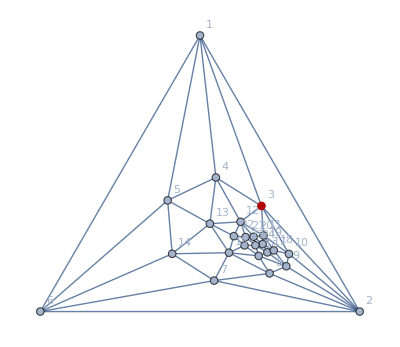

```mathematica
Graph[plantri[[10000]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{3}]
```

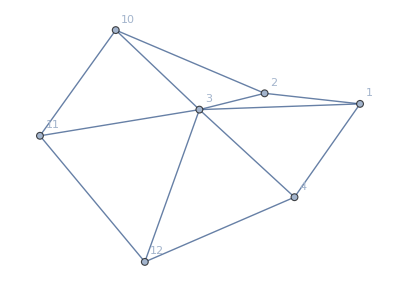

```mathematica
With[
{g=Graph[plantri[[10000]]]},
Graph[NeighborhoodGraph[g,3],VertexLabels->"Name"]
]
```

```mathematica
With[
{g=Graph[plantri[[10000]]]},
Table[{v->{VertexDegree[g,v],VertexList[NeighborhoodGraph[g,v]]}},{v,VertexList[g]}]
]
```

{{1→{5,{1,2,3,4,5,6}}},{2→{7,{2,1,3,6,7,8,9,10}}},{3→{6,{3,1,2,4,10,11,12}}},{4→{5,{4,1,3,5,12,13}}},{5→{5,{5,1,4,6,13,14}}},{6→{5,{6,1,2,5,7,14}}},{7→{5,{7,2,6,8,14,15}}},{8→{5,{8,2,7,9,15,16}}},{9→{6,{9,2,8,10,16,17,18}}},{10→{5,{10,2,3,9,11,18}}},{11→{6,{11,3,10,12,18,19,20}}},{12→{7,{12,3,4,11,13,20,21,22}}},{13→{6,{13,4,5,12,14,15,22}}},{14→{5,{14,5,6,7,13,15}}},{15→{7,{15,7,8,13,14,16,22,23}}},{16→{6,{16,8,9,15,17,23,24}}},{17→{5,{17,9,16,18,19,24}}},{18→{5,{18,9,10,11,17,19}}},{19→{5,{19,11,17,18,20,24}}},{20→{5,{20,11,12,19,21,24}}},{21→{5,{21,12,20,22,23,24}}},{22→{5,{22,12,13,15,21,23}}},{23→{5,{23,15,16,21,22,24}}},{24→{6,{24,16,17,19,20,21,23}}}}

## Planarity criterium

make a criterium for variables x and y to lie on the point between p1 and p2

```mathematica
MakeLineSegmentCrit[p1_,p2_, what_, x_, y_]:=Block[{result=True,diffx,diffy, back=Association[]},
If[p1[[1]]<p2[[1]],
result=p1[[1]]<x<p2[[1]],
If[p1[[1]]>p2[[1]],
result=p2[[1]]<x<p1[[1]],
result=x==p1[[1]]
]
];
If[p1[[2]]<p2[[2]],
result=result&&p1[[2]]<y<p2[[2]],
If[p1[[2]]>p2[[2]],
result=result&&p2[[2]]<y<p1[[2]],
result=result&&y==p1[[2]]
]
];
diffx=p2[[1]]-p1[[1]];
If[diffx≠0,
diffy=p2[[2]]-p1[[2]];
result=result&&((y-p1[[2]])==(diffy/diffx)*(x-p1[[1]]))
,
result=result&&(x==p1[[1]])
];
back["crit"]=result;
back["what"]=what;
back
]
```

The following piece of code sees whether a given graph is planar.  To do so, it creates tow sets of line segments.  The first are the edges of the graph.  The second is a line form each vertex to the position where the uncontrcated vertex was (but on a circle more outward).  None of the endpoints is part of the segment.  Then we look at intersections to see if the graph is planar

```mathematica
MyPlanar[assoc_,key_]:=Block[
{item=assoc[key], emb, pos=Association[],posOuter=Association[], length,lines={},sets,res,line1,line2,crit, found=False,mat,i,j,x,y, challenge},
x=Symbol["abcx"<>ToString[key]];
y=Symbol["abcy"<>ToString[key]];
emb=GraphEmbedding[item["graph"]];
length=Length[Flatten[item["vertexsets"]]];
mat=item["matrix"];
i=1;
Table[
Table[
pos[v]=IntegerPart[100*Round[emb[[i]],0.01]];
,{v,set}
];
i++
,{set,item["vertexsets"]}
];
Table[posOuter[k]=200*{Cos[(2π/length )(length-k+1)+Pi/2],Sin[(2π/length )(k-1)+Pi/2]},{k,length}];
Table[crit=MakeLineSegmentCrit[pos[k],posOuter[k], "Node is outward connected " <> ToString[k],x,y];lines=Append[ lines,crit],{k,length}];

Table[
i=Min[item["vertexsets"][[e[[1]]]]];
j=Min[item["vertexsets"][[e[[2]]]]];
crit=MakeLineSegmentCrit[pos[i],pos[j], "Connection between node " <> ToString[i<->j],x,y ];lines=Append[ lines,crit],
{e,EdgeList[item["graph"]]}
];

(*PrintTemporary["line segments computed : " ,Length[lines]];*)
sets=Subsets[Range[Length[lines]],{2}];
Table[
line1=lines[[s[[1]]]];
line2=lines[[s[[2]]]];
Quiet[
challenge=line1["crit"]&&line2["crit"];
res=NSolve[line1["crit"]&&line2["crit"],{x,y}];
];
If[res≠{},(*Print[key ,": Not planar because of ",s,stubbornForm6[key,"graph"], line1["what"],"  ",line1["crit"], "    ", line2["what"],"   ",  line2["crit"],  "     ", res];*)found=True;Return[True]];
,{s,sets}
];
!found
]
```

## Colours

```mathematica
ColourForKey[assoc_,key_]:=Block[{comp},
If[!KeyExistsQ[assoc[key],"comp"],
Return[Gray],
comp=ToString[assoc[key,"comp"]];
If[comp=="Greater",
Return[Darker[Green]],
If[comp=="GreaterEqual",
Return[Orange],
Return[Darker[Red]]
]
]
]
]
```

```mathematica
AndToTable[and_]:=Table[and[[k]],{k,Length[and]}]
```

```mathematica
InverseKey[assoc_,colofour_]:=First[Select[Keys[assoc],assoc["colofour"]==colofour&]]
```

## Generating graphs directly

```mathematica
VertexSetsFromMatrix[mat_]:=Block[{
result = {}, (* Will contain the vertext sets, a set of sets.  These are order so that 1 comes before 2 etc.*)
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col (* current column in the matrix *)
},
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
todo = Select[todo,#≠col&];
]
]
];
result = Append[result,bucket]
]
];
result
]
```

```mathematica
GraphFromMatrix[mat_,vertexSets_]:=Block[{
edges={},
vertices={},
vertexLabels={},
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col, (* current column in the matrix *)
vertexToVertex=Association[],
newVertexToVertex=Association[],
currentVertex=0,
countNodes=Length[mat],
myvertexSets=vertexSets
},
If[myvertexSets==Null,myvertexSets=VertexSetsFromMatrix[mat]];
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
currentVertex++;
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
vertexToVertex[col]=currentVertex;
todo = Select[todo,#≠col&]
]
]
];
newVertexToVertex[currentVertex]=bucket
]
];

(* now compute the edges *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
If[mat[[row,col]]==1,
edges=Append[edges,Sort[{vertexToVertex[row],vertexToVertex[col]}]]
]
]
];
edges=DeleteDuplicates[edges];
Graph[
Keys[newVertexToVertex],
edges,
VertexLabels->Table[i->StringRiffle[ newVertexToVertex[i],","],{i,Length[Keys[newVertexToVertex]]}],
VertexStyle->Red,
VertexSize->0.1,
VertexCoordinates->MyCircle[myvertexSets,countNodes],
EdgeStyle->{Thickness[0.02],Darker[Darker[Green]]},
ImageSize->{50,50}
]
]
```

```mathematica
MatrixFromGraph[g_]:=Block[{vertices=VertexList[g],mat,length=VertexCount[g]},
mat=Table[
Table[
If[row==col,2,If[EdgeQ[g,row<->col],1,0]]
,{col,length}
]
,{row,length}
]
]
```

```mathematica
allGraphs=Association[];
```

```mathematica
ComputeComp[assoc_,key_]:=Block[{current,g, clique},
current = assoc[key];
g=current["graph"];
current["comp"]=GreaterEqual;
current["compwhy"] = "No IH";
If[MyPlanar[assoc,key],
current["comp"]=Greater;
current["compwhy"] = "This is a planar contraction"
,
(* not planar contraction - look for K5 *)
clique=First[FindClique[g]];
If[Length[clique]≥5,
current["comp"]=Equal;
current["compwhy"] = "This graph contains Clique of size"<> ToString[Length[clique]]
]
];
current
]
```

## Compute color table

the following procedure only works if the vertexset represents a complete graph.

```mathematica
ComputeColorTable[vertexSets_]:=Block[
{vertexCount=Length[Flatten[vertexSets]], combinations, vertexToBucketNumber=Association[],left,right,colofour},

Table[Table[vertexToBucketNumber[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
combinations=Subsets[Range[vertexCount],{2}];
colofour=PartitionToSymbol[vertexSets];
Table[
left=vertexToBucketNumber[c[[1]]];
right=vertexToBucketNumber[c[[2]]];

If[left==right,
{colofour,0},
{0,colofour}
]
,{c,combinations}
]
]
```

```mathematica
globalDepth=1
```

1

```mathematica
ComputeGraph[mat_,depth_]:=Block[{result,row,col,g, matJoin,matContract, rowBucket, colBucket,i,j, vertexSets,current,key,leftKey,rightKey, left, right,vertexSetLength,compressed, fromVertexToVertexSet,size,max,max2},
If[depth≤0,Interrupt[]];
(* first see if we can find it *)
globalDepth=depth;
key=GraphMatrixSignature[mat];

If[KeyExistsQ[allGraphs,key],
current = allGraphs[key];
result=key;
Return[key]
,
(* cannot find it : create an entry *)
vertexSets = VertexSetsFromMatrix[mat];
g=GraphFromMatrix[mat,vertexSets];
current=Association[];
current["signature"]=GraphMatrixSignature[mat];
current["matrix"]=mat;
current["graph"]=g;
current["vertexsets"]=vertexSets;
current["vertices"]=VertexList[g];
current["edges"]=EdgeList[g];
current["relations"]={};
current["links"]={};
current["parents"]={};
current["children"]={};
allGraphs[key]=current;
current=ComputeComp[allGraphs,key];
];

(*If[ToString[current["comp"]]=="Equal",
(* no need to go deeper iw we already have K5 *)
result=key;
current["colofour"]=0;
allGraphs[key]=current;
Return[key]
];*)
g=current["graph"];
vertexSets = current["vertexsets"];
vertexSetLength=Length[vertexSets];
size=Length[Flatten[vertexSets]];

(* see if it is a complete graph *)
If[CompleteGraphQ[g],
(* complete graph - try set comp and compwhy, colofour and colortable*)
result=key;
current["colofour"]=PartitionToSymbol[vertexSets];
current["colortable"]=ComputeColorTable[vertexSets];
,
(*  not a complete graph *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
(*for every vertex couple thatis not connected we compute the connected and the contracted form *)
If[mat[[row,col]]==0,
matJoin=mat;
matContract=mat;

(* first compute to which vertex set row and column belong*)
fromVertexToVertexSet=Association[];
Table[Table[fromVertexToVertexSet[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
rowBucket=vertexSets[[fromVertexToVertexSet[row]]];
colBucket=vertexSets[[fromVertexToVertexSet[col]]];

(* now set the entries in contract and joined *)
Table[
matContract[[r,c]]=2;
matContract[[c,r]]=2;
matJoin[[r,c]]=1;
matJoin[[c,r]]=1
,
{r,rowBucket},
{c,colBucket}
];
(* now make sure the entries are consistent.  We take the max of the other entries *)
Table[
max=Max[Table[matContract[[r,v]],{r, rowBucket}]];
max2=Max[Table[matContract[[r,v]],{r, colBucket}]];
max=Max[max,max2];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, rowBucket}];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, colBucket}];
,
{v,size}
];

(* compute left and right *)
leftKey=ComputeGraph[matJoin,depth-1];
rightKey = ComputeGraph[matContract,depth-1];
left=allGraphs[leftKey];
right=allGraphs[rightKey];

(* if my position is not clear yet, try to see if the children can help *)
If[ToString[current["comp"]]=="GreaterEqual",
If[ToString[left["comp"]]=="Greater"||ToString[right["comp"]]=="Greater",
current["comp"]=Greater;
current["compwhy"]="The relation holds x"<> ToString[key]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>")"
]
];

current["colofour"]=left["colofour"]+right["colofour"];
current["colortable"]=left["colortable"]+right["colortable"];
current["relations"]=Append[current["relations"],Symbol["x"<>ToString[key]]==Symbol["x"<>ToString[leftKey]]+Symbol["x"<>ToString[rightKey]]];
left["relations"]=Append[left["relations"],Symbol["x"<>ToString[leftKey]]==Symbol["x"<>ToString[key]]-Symbol["x"<>ToString[rightKey]]];
right["relations"]=Append[right["relations"],Symbol["x"<>ToString[rightKey]]==Symbol["x"<>ToString[key]]-Symbol["x"<>ToString[leftKey]]];

current["children"]=Append[current["children"],{leftKey,rightKey}];
left["parents"]=Append[left["parents"],key];
right["parents"]=Append[right["parents"],key];

allGraphs[leftKey]=left;
allGraphs[rightKey]=right;
result=key;

(* force a premature stop *)
(*col=size+1;
row=col;*)
]
]
]
];
allGraphs[key]=current;
result
]
```

```mathematica
ColourForRelation[assoc_,father_,childcouple_]:=Block[{
compFather=ToString[assoc[father,"comp"]],
left=ToString[assoc[childcouple[[1]],"comp"]],
right=ToString[assoc[childcouple[[2]],"comp"]]
},
If[compFather=="Greater",
If[left=="Greater" && right == "Equal",
Return[Green]
];
If[right=="Greater" && left == "Equal",
Return[Green]
];
If[left≠"Greater" && right ≠ "Greater",
Return[Blue]
];
];
Return [ColourForKey[assoc,father]]
]
```

```mathematica
DependencyGraph[assoc_,startKey_,rep_:{}]:=Block[{todo={startKey},edges={}, children,currentKey, vertexColors={},vertices={},vertexLabels={},g,mat,size,visited={},currentColor},
If[ListQ[startKey],
todo=startKey;
edges=Table["root"->k,{k,startKey}];
vertices={"root"}
];
Monitor[
While[todo≠{},
currentKey=First[todo];
visited=Append[visited,currentKey];
todo=Rest[todo];
vertices=Append[vertices,currentKey];
currentColor=ColourForKey[assoc,currentKey];
vertexColors=Append[vertexColors,currentKey->currentColor];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
vertexLabels=Append[vertexLabels,currentKey->
Tooltip[
currentKey,
Labeled[
Column[
{
Style[currentKey,Bold],
MatrixForm[mat,TableHeadings->{Table[Style[k,Red],{k,size}],Table[Style[k,Red],{k,size}]}]
,
Row[{
assoc[currentKey]["graph"],
Graph[
VertexList[assoc[currentKey]["graph"]],
EdgeList[assoc[currentKey]["graph"]],
VertexLabels->PropertyValue[assoc[currentKey]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[assoc[currentKey]["children"],Italic],
Style[assoc[currentKey]["colofour"]/.rep,Italic]
},
Center
],Style[assoc[currentKey]["compwhy"],Bold]]]];
children=assoc[currentKey,"children"];
If[ToString[assoc[currentKey]["comp"]]≠"Equal",
Table[
Table[
If[True||!MemberQ[visited,child],
vertexLabels=Append[vertexLabels,childCouple->Tooltip["*",
Column[{
Style[currentKey,Bold,ColourForKey[assoc,currentKey]]
,
Row[{
Style[childCouple[[1]],ColourForKey[assoc,childCouple[[1]]]],
"   ",
Style[childCouple[[2]],ColourForKey[assoc,childCouple[[2]]]]
}
]}]]];
vertexColors=Append[vertexColors,childCouple->ColourForRelation[assoc,currentKey,childCouple]];
edges=Append[edges,childCouple->child];
edges=Append[edges,currentKey->childCouple];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
]
],
{Length[todo],Length[visited]}
];
Graph[
vertices,
DeleteDuplicates[edges],
VertexStyle->DeleteDuplicates[vertexColors], 
VertexLabels->DeleteDuplicates[vertexLabels],
GraphLayout->"RadialEmbedding",
EdgeShapeFunction->GraphElementData[{"HalfFilledArrow","ArrowSize"->.001}]
]
]
```

```mathematica
Problems[assoc_,startKey_]:=Block[{todo={startKey}, children,currentKey, result={},g,mat,size,visited={}},
If[ListQ[startKey],
todo=startKey;
];
Monitor[
While[todo≠{},
currentKey=First[todo];
todo=Rest[todo];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
children=assoc[currentKey,"children"];
Table[
Table[
If[!MemberQ[visited,child],
Block[{
compFather=ToString[assoc[currentKey,"comp"]],
left=ToString[assoc[childCouple[[1]],"comp"]],
right=ToString[assoc[childCouple[[2]],"comp"]]
},
If[compFather=="Greater",
If[left=="GreaterEqual" && right =="GreaterEqual" ,
result=Join[result,Map[currentKey->#&, childCouple]];
];
];
];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
],
Length[todo]
];
Sort[DeleteDuplicates[result]]
]
```

## Propagate and push to get colors correct

```mathematica
PropagateAllGraphs[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs[k];
If[ToString[current["comp"]]=="GreaterEqual",
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs[leftKey];
right=allGraphs[rightKey];
If[ToString[left["comp"]]=="Greater"||ToString[right["comp"]]=="Greater",
current["comp"]=Greater;
current["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated)";
Print[current["compwhy"]];
changed++;
allGraphs[k]=current;
,
If[ToString[left["comp"]]=="Equal"&&ToString[right["comp"]]=="Equal",
current["comp"]=Equal;
current["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
Print[current["compwhy"]];
changed++;
allGraphs[k]=current;
]
]
,{children,allGraphs[k,"children"]}
];
]
,
{k,Keys[allGraphs]}],
k
];
changed
]
```

```mathematica
PushAllGraphs[]:=Block[{leftKey,rightKey,left,right,current,children,changed=0},
Monitor[
Table[
current = allGraphs[k];
If[ToString[current["comp"]]=="Greater" ,
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs[leftKey];
right=allGraphs[rightKey];
If[ToString[left["comp"]]=="Equal"&&ToString[right["comp"]]=="GreaterEqual",
right["comp"]=Greater;
right["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (so this must be >0)";
Print[right["compwhy"]];
changed++;
allGraphs[rightKey]=right;
];
If[ToString[right["comp"]]=="Equal"&&ToString[left["comp"]]=="GreaterEqual",
left["comp"]=Greater;
left["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (so this must be >0)";
Print[left["compwhy"]];
changed++;
allGraphs[leftKey]=left;
],
{children,allGraphs[k,"children"]}]
];

If[ToString[current["comp"]]=="Equal" ,
Table[
Table[
leftKey=child;
left=allGraphs[leftKey];
If[ToString[left["comp"]]!="Equal",
left["comp"]=Equal;
left["compwhy"]="The parent x"<> ToString[k]<> " is zero (so this must be ==0)";
Print[left["compwhy"]];
changed++;
allGraphs[leftKey]=left;
]
,{child,children}
];
,
{children,allGraphs[k,"children"]}]
]
,
{k,Keys[allGraphs]}],
k
];
changed
]
```

```mathematica
ForceZero[key_]:=Block[{result=0},
If[ToString[allGraphs[key,"comp"]]≠"Equal",
If[ToString[allGraphs[key,"comp"]]=="Greater",
Print["Problem with key ", key];
Interrupt[];
];
allGraphs[key,"comp"]=Equal;
allGraphs[key,"compwhy"]="forced to zero (recursive)";
result+=1;
];
Table[
result+=ForceZero[child]
,{child,Flatten[allGraphs[key,"children"]]}
];
result
]
```

## Embedding in plantri 8

```mathematica
EmbedGraphInPlantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

## Laplacian of a graph

Computes the first cofactor, which is the determinant of th ematrix without first row and forst column

```mathematica
FirstCoFactor[matrix_]:=Det[Rest[Map[Rest,matrix]]]
```

The degree matriix is a diagonal matrix where each diagonal entry contains the vertext degree of that vertex.

```mathematica
DegreeMatrix[g_]:=Block[{},
Table[
Table[If[v1==v2,VertexDegree[g,v1],0],{v1,VertexList[g]}],{v2,VertexList[g]}
]
]
```

```mathematica
GraphLaplacian[g_]:=DegreeMatrix[g]-AdjacencyMatrix[g]
```

```mathematica
NumberOfSpanningTrees[g_]:=FirstCoFactor[GraphLaplacian[g]]
```

## Comparing partition symbols

```mathematica
RemoveMin[s_]:=Block[{set1,min},
(* first make strings into lists of integers*)
set1=Map[Map[FromDigits[#]&, StringPartition[#,1]]&,StringSplit[s,"x"]];
(* now find the minimum *)
min=Min[Flatten[set1]];
(*remove the minimum for the bucket that contains it *)
set1=Map[Select[#,#≠min&]&,set1];
(* if a bucket is now empty, remove it *)
set1=Select[set1,#≠{}&];
(* now stich the buckets together as a string *)
set1=Map[StringJoin[ Map[ToString[#]&,#]]&,set1];
StringRiffle[set1,"x"]
]
```

PartitionToSets will convert a string like 123x45 into {{1,2,3},{4,5}}.  PartitionToLength Will count the number of chunks  of a given length in a partition.  This vector of chunklength counts is then interpreted as a number in order to be able to efficiently sort symbols.

```mathematica
PartitionToSets[partition_]:=Block[{splitted,temp},
splitted=StringSplit[partition,"x"];
temp=Map[StringPartition[#,1]&,splitted];
Map[Map[FromDigits[#,10]&,#]&,temp]
]
```

```mathematica
PartitionToLength[p1_]:=Block[
{
c1=PartitionToSets[p1],
v1,
l
},
l=Length[Flatten[c1]];
v1=Table[0,{k,1,l}];
Table[
v1[[Length[chunk]]]+=1
,
{chunk,c1}
];
FromDigits[Reverse[v1],l]
]
```

```mathematica
BaseVarComp2[v1_,v2_]:=Block[{s1,s2,l1,l2,val1,val2},
If[v1==v2,Return[False]];
s1=StringDrop[SymbolName[v1],1];
s2=StringDrop[ SymbolName[v2],1];
l1=StringCount[s1,"x"];
l2=StringCount[s2,"x"];
If[l1≠l2,
l1<l2,
val1=PartitionToLength[s1];
val2=PartitionToLength[s2];
If[val1≠val2,
val1>val2,
TrueQ[s1<s2]
]
]
]
```

## Drawing some mobius - like graphs lattice graphs

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{sets,result=False,merged},
sets=Subsets[sets2,{2}];
Table[
merged=Sort[Join[s[[1]],s[[2]]]];
If[MemberQ[sets1,merged],
result=True
(*Print["Not member",merged, " from ",sets1]*)
]
,
{s,sets}];
result
]
```

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{result=True,merged,allOK},
Table[
If[Length[Select[sets1,Length[Intersection[#,s]]==Length[s]&]]≠1,
result=False;
]
,
{s,sets2}];
result
]
```

```mathematica
DropMore[symbol_,n_]:=Block[{name=SymbolName[symbol],result,mult=1, current=Null,node,max},
result=name;
max=StringLength[StringDelete[name,"x"]]-1;
For[current=max,current> n, current--,
node=ToString[current];
If[StringEndsQ[result,"x"<>node],
mult*=(n-1);result=StringDrop[result,-2],
result=StringDelete[result,node]
];
If[StringEndsQ[result,"x"],
Interrupt[];
result=StringDrop[result,-1]
];
];
Simplify[mult*Symbol[result]]
]
```

```mathematica
MobiusGraph4[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

## First read five and six and compute their null atoms

```mathematica
allGraphs2=Get["d:\\saved\\allGraphs2-realnull.m"];
```

```mathematica
allGraphs3=Get["d:\\saved\\allGraphs3-realnull.m"];
```

```mathematica
allGraphs4=Get["d:\\saved\\allGraphs4-realnull.m"];
```

```mathematica
allGraphs5=Get["d:\\saved\\allGraphs5-realnull.m"];
```

```mathematica
allGraphs6=Get["d:\\saved\\allGraphs6-realnull.m"];
```

```mathematica
allGraphs2NullAtomKeys=Select[Keys[allGraphs2],Length[ListofVars[allGraphs2[#,"colofourrealnull"]]]==1&];Length[allGraphs2NullAtomKeys]
```

2

```mathematica
allGraphs2AtomKeys=Select[Keys[allGraphs2],Length[ListofVars[allGraphs2[#,"colofour"]]]==1&];Length[allGraphs2AtomKeys]
```

2

```mathematica
allGraphs3NullAtomKeys=Select[Keys[allGraphs3],Length[ListofVars[allGraphs3[#,"colofourrealnull"]]]==1&];Length[allGraphs3NullAtomKeys]
```

5

```mathematica
allGraphs3AtomKeys=Select[Keys[allGraphs3],Length[ListofVars[allGraphs3[#,"colofour"]]]==1&];Length[allGraphs3AtomKeys]
```

5

```mathematica
allGraphs4NullAtomKeys=Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofourrealnull"]]]==1&];Length[allGraphs4NullAtomKeys]
```

15

```mathematica
allGraphs4AtomKeys=Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofour"]]]==1&];Length[allGraphs4AtomKeys]
```

15

```mathematica
allGraphs5NullAtomKeys=Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourrealnull"]]]==1&];Length[allGraphs5NullAtomKeys]
```

52

```mathematica
allGraphs5AtomKeys=Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofour"]]]==1&];Length[allGraphs5AtomKeys]
```

52

```mathematica
allGraphs6NullAtomKeys=Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,"colofourrealnull"]]]==1&];Length[allGraphs6NullAtomKeys]
```

203

```mathematica
allGraphs6AtomKeys=Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,"colofour"]]]==1&];Length[allGraphs6AtomKeys]
```

203

```mathematica
K3Key=First[Select[Keys[allGraphs3],With[{g=allGraphs3[#,"graph"]},VertexCount[g]==3&&EdgeCount[g]==3]&]]
```

13

```mathematica
K4Key=First[Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==6]&]]
```

364

```mathematica
K5Key=First[Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&EdgeCount[g]==10]&]]
```

29524

```mathematica
K6Key=First[Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==15]&]]
```

7174453

## Calculating the mobius Function of a partition lattice

```mathematica
SubSetQ[large_,small_]:=Sort[Intersection[large,small]]==Sort[small]
```

```mathematica
MobiusValue[partition1_,partition2_]:=Block[{
c1=Length[partition1],
c2=Length[partition2], 
sorted1=Sort[Map[Sort,partition1]], 
sorted2=Sort[Map[Sort,partition2]],
counts,
counts2,
position,
found,
foundFactor=1
},
If[c1==c2,
If[sorted1==sorted2,1,0]
,
If[c1>c2,
counts=Table[0,c2];
Table[
position=1;
found=False;
Table[
If[SubsetQ[largeSet, smallSet],
counts[[position]]=counts[[position]]+1;
found=True
,{largeSet,sorted2}
];
position++;,
{largeSet,sorted2}
];
If[!found,foundFactor=0]
,{smallSet, sorted1}
];
counts2=Map[If[#==0,0,(#-1)!]&,counts];
foundFactor*Apply[Times,counts2]*(-1)^(c1-c2)
,
0
]
]
]
```

```mathematica
BlockToSet[b_]:=Block[{result={},pos},
result=Table[
FromDigits[c],
{c,Characters[b]}];
result
]
```

```mathematica
StringToPartition[s_]:=Block[{result={}, blocks=StringSplit[s,"x"]},
result=Table[
BlockToSet[b]
,{b,blocks}
];
result
]
```

```mathematica
PartitionFaculty[p_]:=Fold[Times,Map[Length[#]!&,p]]
```

```mathematica
(*CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
c1=StringCount[str1,"x"];
c2=StringCount[str2,"x"];
If[c1≠c2,
Greater[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]*)
```

```mathematica
CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2,p1,p2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
p1=StringToPartition[str1];
p2=StringToPartition[str2];
c1=PartitionFaculty[p1];
c2=PartitionFaculty[p2];
If[c1≠c2,
Less[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
MobiusMatrix[allGraphs_]:=Block[{
allNull=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&],
allNullSorted},
allNullSorted=Sort[allNull,CompareSymbols[allGraphs[#1,"colofourrealnull"],allGraphs[#2,"colofourrealnull"]]&];
Monitor[
Table[
MobiusValue[allGraphs[i,"vertexsets"],allGraphs[j,"vertexsets"]]
,{i,allNullSorted},{j,allNullSorted}
],
{i,j}
]
];
```

```mathematica
MobiusMatrixFromSets[vertexSets_]:=Block[{},
Monitor[
Table[
MobiusValue[i,j]
,{i,vertexSets},{j,vertexSets}
],
{i,j}
]
]
```

## Finding a graph complement

```mathematica
FindComplement[key_,allGraphs_]:=Block[{compl, g, rest},
g=allGraphs[key,"graph"];
compl=GraphComplement[g];
rest=Select[allGraphs,#["vertexsets"]==allGraphs[key,"vertexsets"]&];
rest=Select[rest,VertexCount[#["graph"]]==VertexCount[compl]&&EdgeCount[#["graph"]]==EdgeCount[compl]&];
Table[
rest=Select[rest,EdgeQ[#["graph"],e]&]
,{e,EdgeList[compl]}
];
First[Keys[rest]]
]
```

## Some partition helpers

```mathematica
SymbolToLabel[s_]:=Row[Riffle[ StringSplit[StringDrop[SymbolName[s ],1],"x"],Style["|",Bold,Red]]]
```

```mathematica
PartitionToLabel[s_]:=Row[Riffle[ Map[SetToString[#]&,s],Style["|",Bold,Red]]]
```

The following method calculates the vertex partitions that are coloured red, blue or green inside the complete partition lattice.

```mathematica
RedBlueGreen[key_,allGraphs_]:=Block[{
red=Map[SymbolToLabel[#]&,ListofVars[allGraphs[key,"colofourrealnull"]]]//Sort,
blue=Map[SymbolToLabel[#]&,ListofVars[allGraphs[key,"colofour"]]]//Sort,
all=Map[SymbolToLabel[#]&,ListofVars[allGraphs[0,"colofour"]]]//Sort,
green
},
green=all;
Table[green=Select[green,ToString[#]≠ToString[r]&],{r,red}];
Table[green=Select[green,ToString[#]≠ToString[b]&],{b,blue}];
green=Sort[green];
{red,blue,green}
]
```

## Painting blue nodes structures (complete graph formula)

```mathematica
SymbolToSets[s_]:=Map[Map[FromDigits[#]&,Characters[#]]&,StringSplit[StringDrop[SymbolName[s ],1],"x"]]
```

```mathematica
SetsToSymbol[s_]:=Symbol["v"<>StringRiffle[Map[StringJoin[Map[ToString,#]]&,s],"x"]]
```

```mathematica
FormulaGraph[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> SymbolToLabel[ SetsToSymbol[s]],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

## Find the full formula directly from the graph using the additive procedure

```mathematica
FindFullFormula[g_,v_]:=Block[{edge,pos1,pos2,v2},
If[CompleteGraphQ[g],
{SetsToSymbol2[v]},
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
Join[
FindFullFormula[EdgeAdd[g,edge],v],
FindFullFormula[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
]
]
```